# Quantifying the influence of Urban Design on Quality of Life

## Setup

### Utility Functions

```mathematica
AssociationKeyRename[a_, old_ -> new_] /; KeyExistsQ[a, old] := KeyDrop[old] @ Append[a, new -> a[old]];
AssociationFromPair[strAndNum_List] := strAndNum⟦1⟧ -> strAndNum⟦2⟧;
AssociationsFromPair[keys_List, vals_List] := MapThread[(#1 -> #2) &, {keys, vals}];
RangeMakeAround[num_Integer, delta_Integer] := Range[num - delta, num + delta];
NomalizeNumber[number_Integer] := number;
NomalizeNumber[number_Rational] := N[number];
NomalizeNumber[number_Real] := number;
NomalizeNumber[number_List] := number⟦1⟧;
NomalizeNumber[number_Quantity] := QuantityMagnitude[number];
NomalizeNumber[number_] := 0;
RescaleIntoInterval[numbers_List, numberNewSmallest_, numberNewLargest_] := Map[(# * (numberNewLargest - numberNewSmallest) + numberNewSmallest) &, Rescale[numbers]];
RescaleIntoInterval[numbers_List] := RescaleIntoInterval[numbers, 0.5, 0.95];

ColorsFindInImage[imgPixels_List, colors_List] := Flatten[Join[Map[(Position[imgPixels, #]) &, colors]]];
ColorsMakeShade[redVals_List, greenVals_List, blueVals_List] := Tuples[{redVals, greenVals, blueVals, { 255 }}];
ColorsMakeShade[red_Integer, green_Integer, blue_Integer, delta_Integer] := ColorsMakeShade[RangeMakeAround[red, delta],RangeMakeAround[green, delta],RangeMakeAround[blue, delta]];
ColorsMakeShade[grey_Integer, delta_Integer] := ColorsMakeShade[grey, grey, grey, delta];
ColorMake[r_,g_,b_] := RGBColor[r/255, g/255, b/255];
ColorMake[parts_List] := ColorMake[parts⟦1⟧, parts⟦2⟧, parts⟦3⟧];

ShuffleSynchronously[listOfLists_List] := Module[{newOrder, lengthShortest},
	lengthShortest = Min[Map[Length, listOfLists]];
	newOrder = RandomSample[Range[lengthShortest]];
	Map[Permute[#, newOrder] &, listOfLists]
];
EqualizeImages[imgs_List] := Module[{smallestW, smallestH, sizes},
	sizes = Map[ImageDimensions, imgs];
	smallestW = Min[sizes⟦All, 1⟧];
	smallestH = Min[sizes⟦All, 2⟧];
	Map[ImageCrop[#, {smallestW, smallestH}] &, imgs]
];
MapReconstructFromImages[imgs_List] := Module[{cntSide, imgsTable}, 
	cntSide = Sqrt[Length[imgs]];
	imgsTable = ArrayReshape[imgs, {cntSide,cntSide}];
	ImageAssemble[imgsTable]
];
```

### General Constants

```mathematica
SetDirectory["/Users/ashvardanian/CodeMine/WolframSummer19/"];
constantPathTweets = "Data/Tweets";
constantPathFeatures = "Data/Features";
constantPathMaps = "Data/Maps";
constantPathSatellites = "Data/Satellites";
constantCityDiameterKM = 10;
constantCityGridSize = 5;
constantShareTraining = 0.9;
constantColorsPerPurpose = Association[{
	"Street" -> {{254,254,254}}, 
	"Highway" -> {{232,208,174}, {227,160,54}, {242,196,99}},
	"Water" -> {{158,197,226}},
	"Park" -> {{201,224,185}, {196,211,192}(*walking trails*)},
	"Train" -> {{148,148,148}},
	"Interesting" -> {{251,248,228}, {240,236,228}(*sports*)},
	"Building" -> {{232,226,212}, {235,233,231}, {192,186,175}, {207,200,188}},
	"Annotations" -> {{69,69,69}, {117,117,117}, {63,63,63}, {88,88,88}}
}];
```

### City Lists

```mathematica
(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
CityRowParse[cityRow_List] := { Interpreter["City"][StringJoin[cityRow⟦2⟧, ", ", cityRow⟦3⟧]], cityRow⟦1⟧ };
citiesWRanks = Map[CityRowParse, Drop[Import["Data/Inputs/CitiesMercer2019.csv"], 1]];
citiesPopular = citiesWRanks⟦All, 1⟧;
citiesPositivness = RescaleIntoInterval[Map[(N[1/#]) &, citiesWRanks⟦All, 2⟧]];
```

```mathematica
TakeLargestNCitiesFrom[citiesAll_, count_Integer] := Module[{citiesWStats},
	citiesWStats = Map[{#,CityData[#,"Population"]} &, citiesAll];
	citiesWStats = DeleteCases[citiesWStats,{_,_Missing}];
	citiesWStats = Reverse[SortBy[citiesWStats,Last]];
	Take[citiesWStats, UpTo[count]]⟦All, 1⟧
];
citiesLargest = TakeLargestNCitiesFrom[CityData[All], 100];
citiesUnpopular = Complement[citiesLargest, citiesPopular];
```

```mathematica
CityName[city_] := EntityValue[city, "Name"];
CityBoundsAround[cityCenter_] := Normal[GeoBoundingBox[cityCenter, Quantity[constantCityDiameterKM, "Kilometers"]]];
CityBounds[city_] := CityBoundsAround[GeoCenter[city]];
CityDataPath[directory_String, city_String] := StringJoin[{directory, "/", city, ".mx"}];
CityDataPath[directory_String, city_] := CityDataPath[directory, CityName[city]];
```

## Intro

### Problem Definition

Most of the population around the globe is now concentrated in cities. Cities provide the environment for collaboration and scientific discoveries.
There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.

```mathematica
problemGoodCitiesGDP = Quiet[Total[ExtractGDPs[citiesPopular]]];
problemBadBigCitiesGDP = Quiet[Total[ExtractGDPs[citiesUnpopular]]];
problemGlobalGDP = Total[Map[#["GDP"] &, CountryData[All]]]⟦2⟧;
```

```mathematica
Echo@ StringTemplate["We have analyzed `` cities with combined GDP of ``. It accounts for `` of global economy."][
	(Length[citiesPopular] + Length[citiesLargest]),
	(problemGoodCitiesGDP + problemBadBigCitiesGDP),
	(problemGoodCitiesGDP + problemBadBigCitiesGDP) / problemGlobalGDP
];
```

We have analyzed 200 cities with combined GDP of $13528044528286. per year. It accounts for 0.167549 of global economy.

### Quality of Life

The problem just gets harder once we realize, that there is no obvious metric for quality of life. For simplicity purposes, we will use existing rankings of cities. Our primary ranking was “2019 Quality of Living survey” by Mercer. They compare hundreds of cities but only publish the top 100 of them. We have extended that list with some counter-examples. Namely, the largest cities on the planet, not included in the original list.

### Plan

Linear models and why they don’t work?

Non-linear models and why they don't work?

Observed correlations and future work.

## Data Crawling

### Twitter

```mathematica
ExtractTweets[city_] := Normal[tw["TweetSearch", "Query"->CityName[city]]];
ExportTweets[city_] := Export[CityDataPath[constantPathTweets, city],ExtractTweets[city]];
ImportTweets[city_] := Import[CityDataPath[constantPathTweets, city]];
```

### Maps

```mathematica
ExtractMapsGrid[city_, cityCenter_] := Module[{cityBounds, gridLats, gridLons, cityParts, MakeCell},
	cityBounds = CityBoundsAround[cityCenter];
	gridLats = Subdivide[Latitude[cityBounds⟦1⟧],Latitude[cityBounds⟦2⟧], constantCityGridSize+1];
	gridLons = Subdivide[Longitude[cityBounds⟦1⟧],Longitude[cityBounds⟦2⟧], constantCityGridSize+1];
	MakeCell[i_Integer, j_Integer] := GeoRange[{gridLats⟦i⟧, gridLats⟦i+1⟧}, {gridLons⟦j⟧, gridLons⟦j+1⟧}];
	cityParts = Flatten[Table[MakeCell[i, j], {i, constantCityGridSize}, {j, constantCityGridSize}]];
	cityParts
];
ExtractMaps[city_] := Module[{cityParts, cityCenter, ImageForCell},
	cityCenter = GeoPosition[city];
	cityParts = ExtractMapsGrid[city, cityCenter];
	ImageForCell[coords_] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[GeoRange->coordsAsList]]
	];
	EqualizeImages[Map[ImageForCell, cityParts]]
];
ExportMaps[city_] := Export[CityDataPath[constantPathMaps, city],ExtractMaps[city]];
ImportMaps[city_] := Import[CityDataPath[constantPathMaps, city]];
```

### Satellites

```mathematica
ExtractSatellites[city_] := Module[{cityCenter, cityParts, ImageForCell},
	cityCenter = GeoPosition[city];
	cityParts = ExtractMapsGrid[city, cityCenter];
	ImageForCell[coords_, rotation_Real] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[
                GeoRange -> coordsAsList, 
                GeoProjection -> {"ObliqueMercator", "Centering" -> {cityCenter, rotation}},
                GeoBackground -> GeoStyling["StreetMap"], 
                GeoServer -> "http://mt0.google.com/vt/lyrs=s,h&x=`2`&y=`3`&z=`1`"]]
	];
	EqualizeImages[Join[
		Map[ImageForCell[#, 30.0] &, cityParts],
		Map[ImageForCell[#, 45.0] &, cityParts],
		Map[ImageForCell[#, 90.0] &, cityParts]
	]]
];
ExportSatellites[city_] := Export[CityDataPath[constantPathSatellites, city],ExtractSatellites[city]];
ImportSatellites[city_] := Import[CityDataPath[constantPathSatellites, city]];
```

### Features Extraction

```mathematica
ExtractGDPs[cities_List] := Module[{countries},
	countries = Map[#["Country"] &, cities];
	Map[(cities[[#]]["Population"]*countries[[#]]["GDP"]/countries[[#]]["Population"]) &, Range[Length[cities]]]
];
```

```mathematica
ExtractListFeatures[object_, props_List] := Normal[Map[({#, Normal[object[#]]}) &, props]];
ExtractCityStatsFeatures[city_] := Module[{props}, 
	props = {
		"Population","Latitude","Longitude","Elevation","MagneticFieldStrength"
	};
	Association[Map[AssociationFromPair, ExtractListFeatures[city, props]]]
];
ExtractCountryStatsFeatures[city_] := Module[{
		props, country, 
		countryPopulation, countryArea, 
		propsToNormalizeWPopulation, propsToNormalizeWArea,
		pairsList
	},
	country = city["Country"];
	countryArea = country["Area"];
	countryPopulation = country["Population"];
	props = {
		"Population","Latitude","Longitude",
		"Area","WaterArea","BoundaryLength","CoastlineLength","WaterwayLength",
		"ContributingFamilyWorkers",
		"GDPPerPersonEmployed","GiniIndex","InterestRateSpread","PovertyHeadcount","UnemploymentRate",
		"BookTitles","IlliteracyFraction",
		
		"MaleLifeExpectancy","MaleMedianAge","FemaleLifeExpectancy","FemaleMedianAge",
		"HospitalBedsPer10000Population"
	};
	propsToNormalizeWArea = { };
	propsToNormalizeWPopulation = {
		"Army","HIVAIDSPopulation","ElectricityTotal",
		"ChildPopulation","ElderlyPopulation","AnnualMarriages","AnnualDivorces",
		"NetIncomeFromAbroad","GovernmentDebt","GovernmentSurplus","ImportsValue","ExportsValue",
		"LeisureArrivals","NewspaperTitles"
	};
	pairsList = Join[ExtractListFeatures[country, props], 
		Map[({#⟦1⟧, #⟦2⟧ / countryArea}) &, ExtractListFeatures[country, propsToNormalizeWArea]],
		Map[({#⟦1⟧, #⟦2⟧ / countryPopulation}) &, ExtractListFeatures[country, propsToNormalizeWPopulation]]];
	pairsList = Map[({StringJoin[{"Country", #⟦1⟧}], #⟦2⟧}) &, pairsList];
	Association[Map[AssociationFromPair, pairsList]]
];
ExtractMapFeaturesFromPixels[city_] := Module[{imgQuantized, pixelsList, freqOfColors, imgMerged},
	imgMerged = MapReconstructFromImages[ImportMaps[city]];
	imgQuantized = RemoveAlphaChannel[ColorQuantize[imgMerged, Map[ColorMake, Flatten[Values[constantColorsPerPurpose], {1, 2}]]]];
	pixelsList = Flatten[ImageData[imgQuantized, "Byte"], 1];
	freqOfColors = AssociationMap[(Length[ColorsFindInImage[pixelsList, constantColorsPerPurpose[#]]] / Length[pixelsList]) &, Keys[constantColorsPerPurpose]];
	freqOfColors
];
ExtractMapFeaturesFromOSM[city_] := Module[{cityBounds, osmData, osmNodes, osmWays, parsedWays, graphWays},
	cityBounds = GeoBoundingBox[GeoPosition[city],Quantity[0.5, "Kilometers"]];
	osmData = ResourceFunction["OSMImport"][cityBounds];
	osmNodes = Map[Lookup[#, "Position"] &, osmData["Nodes"]];
	osmWays = Map[Lookup[osmNodes, Lookup[#, "Nodes"]] &, Select[osmData["Ways"], MemberQ[Keys[#Tags],"highway"] &]];
	parsedWays = Flatten[Map[UndirectedEdge@@@Partition[#,2,1] &, Values[osmWays]]];
	graphWays = Graph[parsedWays];
	Association[{
		"MeanNeighborDegree" -> Mean[MeanNeighborDegree[graphWays]],
		"DegreeCentrality" -> Mean[DegreeCentrality[graphWays]],
		"ClosenessCentrality" -> Mean[ClosenessCentrality[graphWays]]
	}]
];
```

### Features Post-processing

```mathematica
ExtractAllFeatures[city_] := Merge[{ 
	ExtractCityStatsFeatures[city], ExtractCountryStatsFeatures[city], 
	ExtractMapFeaturesFromPixels[city], ExtractMapFeaturesFromOSM[city]
	}, Total];
ExportAllFeatures[city_] := Export[CityDataPath[constantPathFeatures, city], ExtractAllFeatures[city]];
ImportAllFeatures[city_] := Import[CityDataPath[constantPathFeatures, city]];
ImportAllFeaturesClean[city_] := Module[{raw, keys, vals},
	raw = ImportAllFeatures[city];
	keys = Keys[raw];
	vals = Map[N[NomalizeNumber[#]] &, Values[raw]];
	AssociationsFromPair[keys, vals]
];
NormalizeFeatures[rowsPerSample_List] := Module[{rowsPerFeature, rowsPerFeatureNormalized},
	rowsPerFeature = Transpose[rowsPerSample];
	rowsPerFeatureNormalized = Map[RescaleIntoInterval, rowsPerFeature];
	Transpose[rowsPerFeatureNormalized]
];
PrepareFeaturesAndNames[cities_List] := Module[{citiesFeatures, citiesFeaturesValues, citiesFeaturesNames},
	citiesFeatures = Map[ImportAllFeaturesClean[#] &, cities];
	citiesFeaturesValues = NormalizeFeatures[Values[citiesFeatures⟦All⟧]]; (*Transform units into raw numbers.*)
	citiesFeaturesNames = First[Keys[citiesFeatures⟦All⟧]];
	{citiesFeaturesValues,  citiesFeaturesNames}
];
```

### Automation

```mathematica
DownloadDataNeeded[city_, loadMaps_, loadSatellites_] := Module[{},
	Echo[StringJoin["Processing city ", CityName[city]]];
	If[!FileExistsQ[CityDataPath[constantPathTweets, city]], ExportTweets[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathMaps, city]] && loadMaps == True, ExportMaps[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathSatellites, city]] && loadSatellites == True, ExportSatellites[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathFeatures, city]], ExportAllFeatures[city], Nothing];
];
```

```mathematica
(*tw = ServiceConnect["Twitter"];
ClearSystemCache[];
Map[DownloadDataNeeded[#, True, True] &, citiesPopular];
Map[DownloadDataNeeded[#, True, False] &, citiesUnpopular];*)
```

## What can be predicted with Twitter?

### Estimating Sentiment

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
EstimateQualityOfLifeWSentiment[data_] := Module[{sentences, tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	sentences = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[sentences];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	{meanPositivness, meanCertainty}
];
```

### Comparing the cities

Once we collect the data from Twitter, we want to see how the

```mathematica
tweetsPerCity = Map[ImportTweets, citiesPopular];
citiesEstimates = Map[EstimateQualityOfLifeWSentiment, tweetsPerCity];
citiesCertainties = RescaleIntoInterval[Map[(#["Value"]) &, citiesEstimates⟦All, 2⟧]];
```

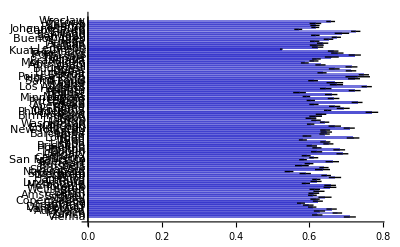

```mathematica
citiesColors = Map[RGBColor[0.2, 0.2, 0.8, #] &, citiesCertainties];
citiesPositivnessFromTweets = citiesEstimates⟦All, 1⟧;
BarChart[citiesPositivnessFromTweets,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

As we can see, there is not much variance between cities, in terms of Tweets sentiment. Our expectation was to see longer bars in the bottom of the chart, but there are no obvious trends on it. Potential reasons:

Lack of relation between the quality of life and sentiment.

Lack of named-entity resolution functionality in Twitter search queries. We can only scrape text from Twitter with substring queries, which often returns results unrelated to cities.

Poor quality of sentiment analyzer. The built-in technology uses a small statistical model trained on a tiny dataset. Larger language modelling systems with attention mechanisms should produce considerably better results.

## Multi-source approach?

Lets compile multiple rankings together, assuming that they have had a more complete model for estimating the quality of life and satisfaction.
For every city we will compose feature vectors containing:

Features extracted from knowledge base;

Features of the enclosing country extracted from knowledge base;

Land-use statistics extracted from rasterized maps;

Metrics of transportation network graph of the city center.

### Linear Regression

```mathematica
FitRegressionRect[rowsPerSample_, predictionsVals_] := Module[{inputNormalized, p, pLinearLayer, pWeights},
	p = Predict[rowsPerSample->predictionsVals, Method->"LinearRegression"];
	pLinearLayer = p⟦1, "Model", "MeanFunction"⟧;
	pWeights = Normal @ pLinearLayer⟦"Arrays"⟧⟦"Weights"⟧;
	pWeights
];
FitRegressionSquare[rowsPerSample_List, predictionsVals_List] := Inverse[Transpose[rowsPerSample].rowsPerSample].Transpose[rowsPerSample].predictionsVals;
RunRegression[weights_List, rowOfSample_List] := Total[Dot[weights, rowOfSample]];
FitRegression[rowsPerSample_, estimatesPerSample_, featuresNames_List] := Module[{
		inputTrain, inputValidate, outputTrain, outputValidate, outputEstimated, 
		modelWights, error, chart, result, trainingCount
	},
	trainingCount = Length[featuresNames];
	inputTrain = Take[rowsPerSample, trainingCount];
	outputTrain = Take[estimatesPerSample, trainingCount];
	inputValidate = Drop[rowsPerSample, trainingCount];
	outputValidate = Drop[estimatesPerSample, trainingCount];
	modelWights = FitRegressionSquare[inputTrain, outputTrain];
	outputEstimated = Map[(RunRegression[modelWights, #]) &, inputValidate];
	error = Norm[outputValidate-outputEstimated, 1] / Length[outputValidate];
	chart = BarChart[modelWights, ChartLabels->featuresNames, BarOrigin->Left, PlotRange->{-5, 5}];

	{error, chart, modelWights}
];
```

### Comparing the cities

```mathematica
citiesFeaturesNamesMaps = Flatten[Join[Keys[ExtractMapFeaturesFromOSM[Entity["City",{"PointAPitre","PointeAPitre","Guadeloupe"}]]], Keys[ExtractMapFeaturesFromPixels[Entity["City",{"PointAPitre","PointeAPitre","Guadeloupe"}]]]]];
citiesFeaturesNamesStats = Flatten[Join[Keys[ExtractCityStatsFeatures[Entity["City",{"PointAPitre","PointeAPitre","Guadeloupe"}]]], Keys[ExtractCountryStatsFeatures[Entity["City",{"PointAPitre","PointeAPitre","Guadeloupe"}]]]]];
```

```mathematica
citiesFeatures = PrepareFeaturesAndNames[RandomSample[citiesPopular]];
citiesFeaturesValues = citiesFeatures⟦1⟧;
citiesFeaturesNames = citiesFeatures⟦2⟧;
```

```mathematica
citiesBlackBoxPredictorOnlyStats = Predict[citiesFeaturesValues⟦All, 1;;Length[citiesFeaturesNamesStats]⟧->citiesPositivness, Method->"LinearRegression"];
citiesBlackBoxPredictorOnlyMaps = Predict[citiesFeaturesValues⟦All, Length[citiesFeaturesNamesStats];;Length[citiesFeaturesNames]⟧->citiesPositivness, Method->"LinearRegression"];
citiesBlackBoxPredictor = Predict[citiesFeaturesValues->citiesPositivness, Method->"LinearRegression"];
citiesBlackBoxPredictorANN = Predict[citiesFeaturesValues->citiesPositivness, Method->"NeuralNetwork"];
```

```mathematica
Grid[{{Information[citiesBlackBoxPredictorOnlyStats], Information[citiesBlackBoxPredictorOnlyMaps], Information[citiesBlackBoxPredictor], Information[citiesBlackBoxPredictorANN]}}]
```

Predictor information
Data type | NumericalVector (length: 40)
Standard deviation | 0.0329 ± 0.0066
Method | LinearRegression
Single evaluation time | 1.72 ms/example
Batch evaluation speed | 145. examples/ms
Loss | -1.48 ± 0.025
Model memory | 224. kB
Training examples used | 100 examples
Training time | 1.51 s
 |  | Predictor information
Data type | NumericalVector (length: 12)
Standard deviation | 0.0303 ± 0.011
Method | LinearRegression
Single evaluation time | 1.31 ms/example
Batch evaluation speed | 353. examples/ms
Loss | -1.74 ± 0.079
Model memory | 222. kB
Training examples used | 100 examples
Training time | 1.14 s
 |  | Predictor information
Data type | NumericalVector (length: 51)
Standard deviation | 0.0307 ± 0.0054
Method | LinearRegression
Single evaluation time | 1.76 ms/example
Batch evaluation speed | 138. examples/ms
Loss | -1.35 ± 0.018
Model memory | 230. kB
Training examples used | 100 examples
Training time | 1.4 s
 |  | Predictor information
Data type | NumericalVector (length: 51)
Standard deviation | 0.0373 ± 0.014
Method | NeuralNetwork
Single evaluation time | 2.44 ms/example
Batch evaluation speed | 40.9 examples/ms
Loss | 6.91 ± 9.7
Model memory | 430. kB
Training examples used | 100 examples
Training time | 5.88 s
 |

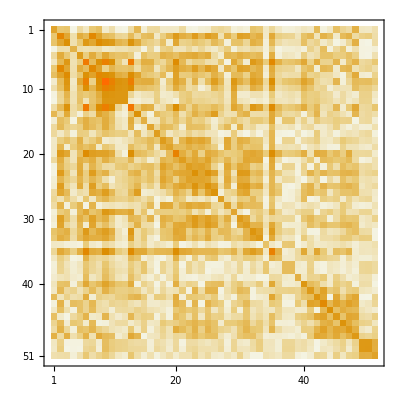

```mathematica
MatrixPlot[Abs[Covariance[PrepareFeaturesAndNames[citiesPopular]⟦1⟧]]]
```

```mathematica
GetRegressionChart[] := Module[{reordered, model},
	reordered = ShuffleSynchronously[{citiesFeaturesValues, citiesPositivness}];
	model = Quiet@FitRegression[reordered⟦1⟧, reordered⟦2⟧, citiesFeaturesNames];
	model⟦2⟧
];
```

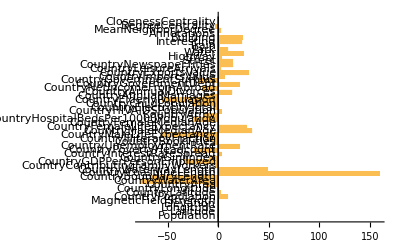

```mathematica
GetRegressionChart[]
```

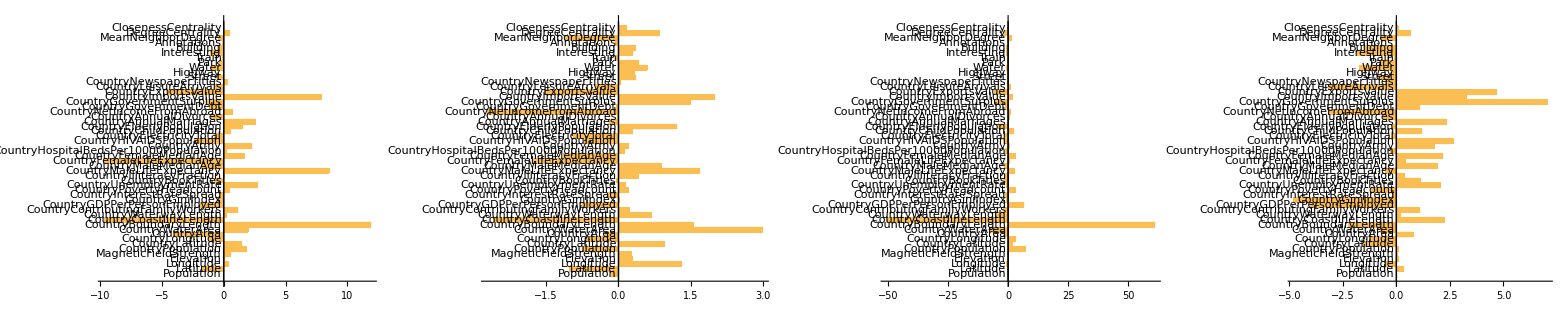

```mathematica
Grid[{Table[GetRegressionChart[], 4]}]
```

```mathematica
Export["PostImageRegression.gif", Table[GetRegressionChart[], 10], "AnimationRepetitions" -> Infinity]
```

PostImageRegression.gif

### Conclusions

Simple Regression models have huge variance and are totally unusable in this setting.

Often we expect non-linear relations between an input factor and predicted value, but such models can’t approximate them.

Non-linear models require a lot more data then 5000 data points.

## Non-linear approach?

Lets see if Convolutional NN models will be able to recognize the patterns, that lie deeper than our manually extracted features.
For that we have collected rasterized maps and satellite images of various regions and augmented them with rotated versions.

### MLP

```mathematica
BuildDataset[city_, rating_Real, imgs_] := Module[{ratings},
	ratings = Table[rating, Length[imgs]];(*Same for all images within city*)
	AssociationsFromPair[imgs, ratings]
];
```

```mathematica
datasetMaps = RandomSample[Flatten[MapThread[BuildDataset[#1, #2, ImportMaps[#1]] &, {citiesPopular, citiesPositivness}]]];
datasetSatellites = RandomSample[Flatten[MapThread[BuildDataset[#1, #2, ImportSatellites[#1]] &, {citiesPopular, citiesPositivness}]]];
```

```mathematica
datasetTrain = Take[datasetMaps, constantShareTraining * Length[datasetMaps]];
datasetValidate = Drop[datasetMaps, constantShareTraining * Length[datasetMaps]];
modelMapsANN = Predict[datasetTrain, Method->"NeuralNetwork", ValidationSet->datasetValidate, TrainingProgressReporting->"Panel"];
```

```mathematica
datasetTrain = Take[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
datasetValidate = Drop[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
modelSatellitesANN = Predict[datasetTrain, Method->"NeuralNetwork", ValidationSet->datasetValidate, TrainingProgressReporting->"Panel"];
```

### Pretrained CNN

Common approach to tackle problems like that is using a model pretrained on a huge dataset and fine-tuning it to your specific problem. The closest model to our task is the huge ResNet-101 model trained on images of places to predict their coordinates. One could try to use some of its internal representations, but our problem is very different from the original one, so the network doesn’t converge.
Training for 8 hours made us reach 30% error rate on training dataset and 55% error on the validation dataset. And the losses stayed around the level 0.7.

```mathematica
modelGeoCNNFull = NetModel["ResNet-101 Trained on YFCC100m Geotagged Data"];
modelGeoCNN = NetFlatten[NetChain[{NetTake[modelGeoCNN, "pool1"], LinearLayer[{}], LogisticSigmoid}], 1];
datasetTrain = Take[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
datasetValidate = Drop[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
modelGeoCNN = NetTrain[modelGeoCNN, Association[{"Input"->Keys[datasetTrain],"Output"->Values[datasetTrain]}], All]
```

NetChain[<>]

## Nice cities vs bad cities?

The sophisticated approaches proved to require a lot more data, that what we can process within the scope of this project. However, we still can see some differences between successfull cities and not so much.

```mathematica
citieslAllFeaturesNormalized = PrepareFeaturesAndNames[Join[citiesPopular, citiesUnpopular]]⟦1⟧;
```

```mathematica
citieslAllFeaturesNormalizedOfGood = citieslAllFeaturesNormalized⟦1;;Length[citiesPopular]⟧;
citieslAllFeaturesNormalizedOfBad = citieslAllFeaturesNormalized⟦Length[citiesPopular]+1;;Length[citiesPopular]+Length[citiesUnpopular]⟧;
```

```mathematica
averagePerFeatureGood = Map[Mean, Transpose[citieslAllFeaturesNormalizedOfGood]];
averagePerFeatureBad = Map[Mean, Transpose[citieslAllFeaturesNormalizedOfBad]];
```

```mathematica
colorsPerFeatureGood = Map[RGBColor[0.2, 0.2, 0.8, If[averagePerFeatureGood[[#]]>averagePerFeatureBad[[#]], 0.8, 0.4]] &, Range[Length[citiesFeaturesNames]]];
colorsPerFeatureBad = Map[RGBColor[0.2, 0.2, 0.8, If[averagePerFeatureGood[[#]]<averagePerFeatureBad[[#]], 0.8, 0.4]] &, Range[Length[citiesFeaturesNames]]];
```

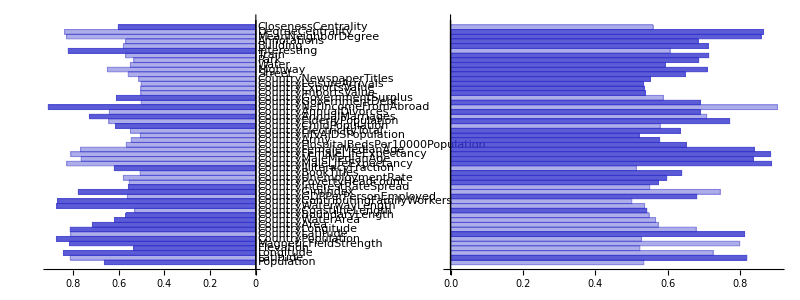

```mathematica
Grid[{{
	BarChart[averagePerFeatureBad,ChartLabels->citiesFeaturesNames,BarOrigin->Right,ChartStyle->colorsPerFeatureBad], 
	BarChart[averagePerFeatureGood,BarOrigin->Left,ChartStyle->colorsPerFeatureGood]
}}]
```

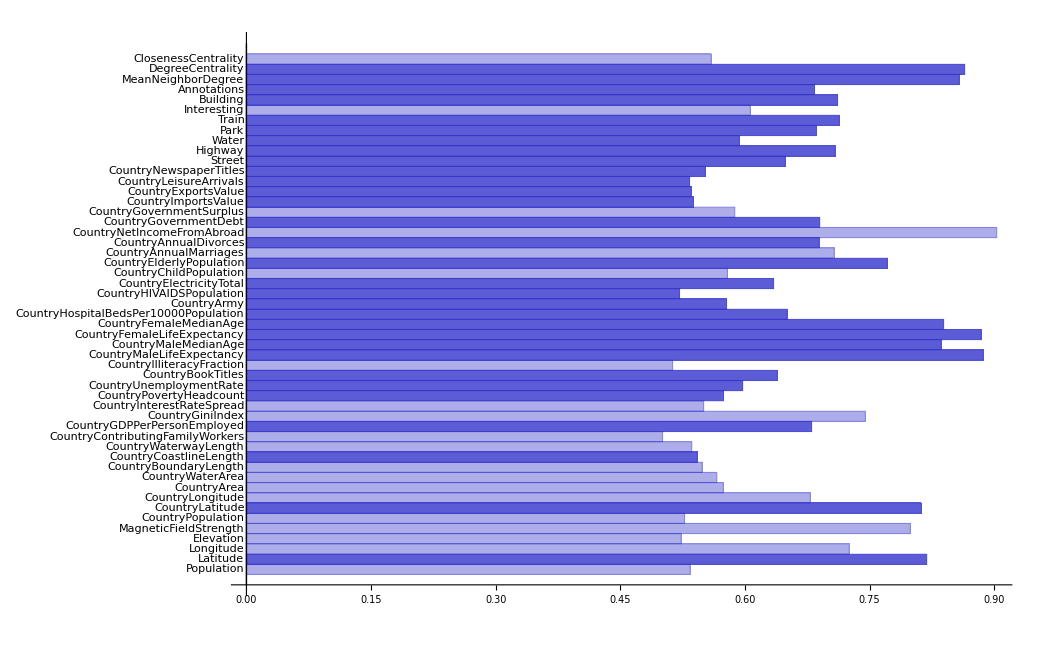

```mathematica
BarChart[averagePerFeatureGood,ChartLabels->citiesFeaturesNames,BarOrigin->Left,ChartStyle->colorsPerFeatureGood]
```

```mathematica
{"gdp per capita", "land use per purpose", "average of country features weighted by city population"}
```

Lets compare the land (per purpose) between differen cities

```mathematica
recognizedLandUsages = Keys[constantColorsPerPurpose];
ExtractLandUsages[city_] := Values[Lookup[ImportAllFeatures[city], recognizedLandUsages]];

BarChart[,ChartLabels->Keys[statsAreaShareByPurpose],BarOrigin->Left]
```